```mathematica
Clear["Global`*"];
SeedRandom[0];
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

Linear Programming Foundations and extensions 
p. 232

```mathematica
A={{-1,-1,-1,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,-1,-1,1,0,0,1,0,0,1,0},
{1,0,0,0,1,0,0,0,0,0,1,0,0,0},
{0,1,0,0,0,0,-1,-1,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,-1,-1,-1,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,-1,-1}};
c={48, 28, 10, 7, 65, 7, 38, 15, 56, 48, 108, 24, 33, 19};
b={0,0,-6,-6,-2,9,5};
```

```mathematica
A//MatrixForm
```

(-1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1)

```mathematica
{u,s,v}=SingularValueDecomposition[A];
```

```mathematica
u//Dimensions
```

{7,7}

```mathematica
s//Dimensions
```

{7,14}

```mathematica
v//Dimensions
```

{14,14}

```mathematica
appendColumn[A_,b_]:=Transpose[Append[Transpose[A],b]];
```

```mathematica
RowReduce[appendColumn[A,b]]//MatrixForm
```

(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -6
0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -6
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -2
0 | 0 | 0 | 1 | 1 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | -14
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
({{1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, -6}, {0, 1, 0, 0, 0, 0, -1, -1, 0, 0, 0, 0, 0, 0, -6}, {0, 0, 1, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 1, -2}, {0, 0, 0, 1, 1, 1, -1, 0, 0, -1, 0, 0, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 1, 0, 1, 1, -14}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -1, -1, 5}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}})
```

{{1,0,0,0,1,0,0,0,0,0,1,0,0,0,-6},{0,1,0,0,0,0,-1,-1,0,0,0,0,0,0,-6},{0,0,1,0,0,1,0,1,0,0,0,0,0,1,-2},{0,0,0,1,1,1,-1,0,0,-1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,1,1,-14},{0,0,0,0,0,0,0,0,0,0,0,1,-1,-1,5},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
LinearProgramming[c,A,-b]
```

{6,6,0,12,0,0,0,0,0,9,0,0,3,2}

```mathematica
RowReduce[appendColumn[A,b]].{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,1}
```

{-6+x1+x11+x5,-6+x2-x7-x8,-2+x14+x3+x6+x8,-x10-x13+x4+x5+x6-x7,-14+x10+x11+x13+x14+x9,5+x12-x13-x14,0}

```mathematica
rep=MapThread[Solve[#1==0,#2][[1]][[1]]&, {{-6+x1+x11+x5,-6+x2-x7-x8,-2+x14+x3+x6+x8,-x10-x13+x4+x5+x6-x7,-14+x10+x11+x13+x14+x9,5+x12-x13-x14},{x1,x2,x3,x4,x9,x12}}]
```

{x1→6-x11-x5,x2→6+x7+x8,x3→2-x14-x6-x8,x4→x10+x13-x5-x6+x7,x9→14-x10-x11-x13-x14,x12→-5+x13+x14}

```mathematica
c.{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14}/.rep//Simplify
```

1140-x10+4 x11+8 x13-23 x14+10 x5-10 x6+73 x7+33 x8

```mathematica
pos=MapThread[Solve[#1==0,#2][[1]][[1]][[2]]&, {{-6+x1+x11+x5,-6+x2-x7-x8,-2+x14+x3+x6+x8,-x10-x13+x4+x5+x6-x7,-14+x10+x11+x13+x14+x9,5+x12-x13-x14},{x1,x2,x3,x4,x9,x12}}]
```

{6-x11-x5,6+x7+x8,2-x14-x6-x8,x10+x13-x5-x6+x7,14-x10-x11-x13-x14,-5+x13+x14}

```mathematica
Map[#>0&,{6-x11-x5,6+x7+x8,2-x14-x6-x8,x10+x13-x5-x6+x7,14-x10-x11-x13-x14,-5+x13+x14}]
```

{6-x11-x5>0,6+x7+x8>0,2-x14-x6-x8>0,x10+x13-x5-x6+x7>0,14-x10-x11-x13-x14>0,-5+x13+x14>0}

```mathematica
LinearSolve[A,-b]
```

{6,6,2,0,0,0,0,0,14,0,0,-5,0,0}

```mathematica
b//Dimensions
```

{7}

```mathematica
FindMinimum[{1,6-x11-x5>0.1&&6+x7+x8>0.1&&2-x14-x6-x8>0.1&&x10+x13-x5-x6+x7>0.1&&14-x10-x11-x13-x14>0.1&&-5+x13+x14>0.1&&x5>0.1&&x6>0.1&&x7>0.1&&x8>0.1&&x10>0.1&&x11>0.1&&x13>0.1&&x14>0.1},{x5,x6,x7,x8,x10,x11,x13,x14}]
```

{1.,{x5→0.1,x6→0.1,x7→0.1,x8→0.1,x10→0.1,x11→0.1,x13→13.6,x14→0.1}}

```mathematica
{6-x11-x5>0,6+x7+x8>0,2-x14-x6-x8>0,x10+x13-x5-x6+x7>0,14-x10-x11-x13-x14>0,-5+x13+x14>0}/.{x5->0.1,x6->0.1,x7->0.1,x8->0.1,x10->0.1,x11->0.1,x13->13.600000000000001,x14->0.1}
```

{True,True,True,True,True,True}

```mathematica
U[x5_,x6_,x7_,x8_,x10_,x11_,x13_,x14_]=
1/100(c.{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14}/.{x1->6-x11-x5,x2->6+x7+x8,x3->2-x14-x6-x8,x4->x10+x13-x5-x6+x7,x9->14-x10-x11-x13-x14,x12->-5+x13+x14}//Simplify);
dU[x5_,x6_,x7_,x8_,x10_,x11_,x13_,x14_]=GradientG[U[x5,x6,x7,x8,x10,x11,x13,x14],{x5,x6,x7,x8,x10,x11,x13,x14}];
ddU[x5_,x6_,x7_,x8_,x10_,x11_,x13_,x14_]=HessianH[U[x5,x6,x7,x8,x10,x11,x13,x14],{x5,x6,x7,x8,x10,x11,x13,x14}];
```

```mathematica
outbnd[{x5_,x6_,x7_,x8_,x10_,x11_,x13_,x14_}]:=AnyTrue[{6-x11-x5,6+x7+x8,2-x14-x6-x8,x10+x13-x5-x6+x7,14-x10-x11-x13-x14,-5+x13+x14},(#<0)&]||AnyTrue[{x5,x6,x7,x8,x10,x11,x13,x14},(#<0)&];
```

```mathematica
Dim=8;
```

```mathematica
INTERVAL=1001;
CHAINS=20;
STEPS=5;
```

```mathematica
qinit=Table[{.1,.1,.1,.1,.1,.1,-.1+13.700000000000001,.1},CHAINS];
dt10=10^-6;
dt20=10^-6;
QS=hmc[U,dU,ddU,Dim,5000,10000,True,False,qinit];
```

100157514.971.29420.6073990.460196264.13457779.1502.960.001156271/1000000True{1,2,3,4,6}{1,6}

200243211.476.43130.3600040.457364263.91943475.3502.960.00204841/1000000True{1,2,4,6}{1,6}

300316662.672.46460.2212420.395551259.12216921.7502.960.003628871/1000000True{1,3,4,6}{1,6}

40045841.2488.25130.2063410.378239258.7546099.99502.960.006428761/1000000True{1,2,3,5,6}{1,6}

50051540.1474.35070.1859450.384712261.5171801.65502.960.009412341/1000000True{1,2,4,5,6}{1,6}

60061535.8190.1850.3801390.479032265.8431801.65502.960.009412341/1000000True{1,2,4,5,6}{1,6}

70071547.6262.13110.5356730.498255254.0341801.65502.960.009412341/1000000True{1,2,4,5,6}{1,6}

80081538.75.29290.3819810.481288263.651801.65502.960.009412341/1000000True{1,2,4,5,6}{1,6}

90091537.3486.78190.3640690.463559264.3141801.65502.960.009412341/1000000True{1,2,4,5,6}{1,6}

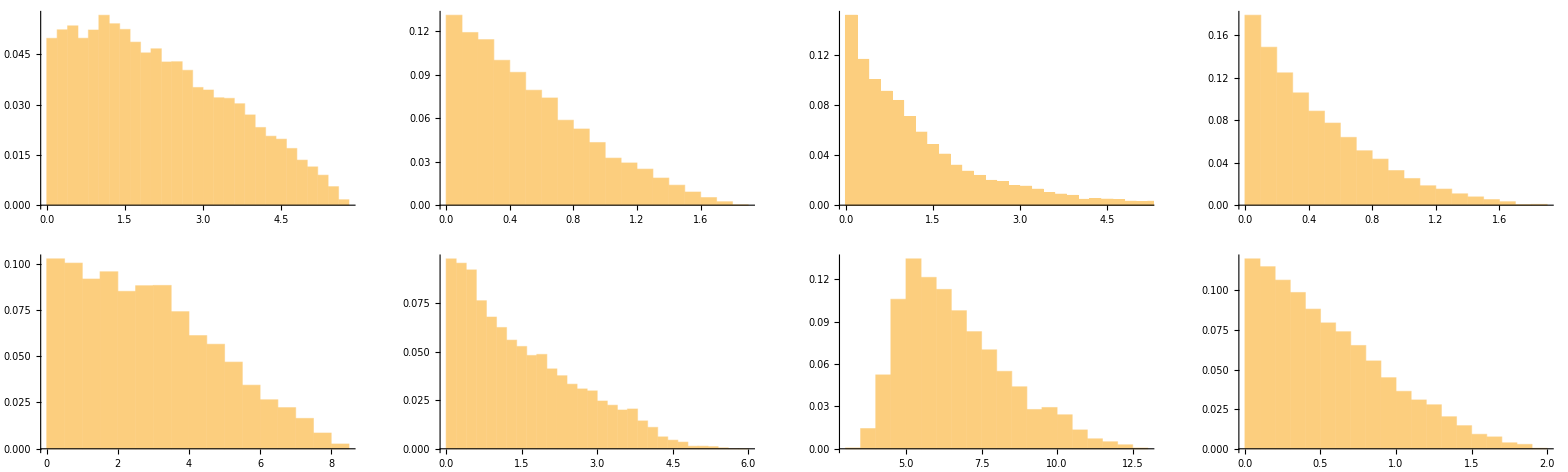

```mathematica
GraphicsGrid[ArrayReshape[Table[Histogram[QS[[;;,i]],Automatic,"Probability"],{i,1,8}],{2,4}]]
```

```mathematica
(*GraphicsGrid[ArrayReshape[Table[ListPlot[QS[[;;,i]],PlotStyle->Opacity[.1]],{i,1,8}],{2,4}]]*)
```

```mathematica
Mean[QS]
```

{2.12828,0.521112,1.26941,0.435128,2.86447,1.49844,6.63435,0.548596}

```mathematica
{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14}/.{x1->6-x11-x5,x2->6+x7+x8,x3->2-x14-x6-x8,x4->x10+x13-x5-x6+x7,x9->14-x10-x11-x13-x14,x12->-5+x13+x14}
```

{6-x11-x5,6+x7+x8,2-x14-x6-x8,x10+x13-x5-x6+x7,x5,x6,x7,x8,14-x10-x11-x13-x14,x10,x11,-5+x13+x14,x13,x14}

```mathematica
QS1=Transpose[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14}/.{x1->6-x11-x5,x2->6+x7+x8,x3->2-x14-x6-x8,x4->x10+x13-x5-x6+x7,x9->14-x10-x11-x13-x14,x12->-5+x13+x14}/.{x5->QS[[;;,1]],x6->QS[[;;,2]],x7->QS[[;;,3]],x8->QS[[;;,4]],x10->QS[[;;,5]],x11->QS[[;;,6]],x13->QS[[;;,7]],x14->QS[[;;,8]]}];
```

```mathematica
QS1//Dimensions
```

{100000,14}

```mathematica
LinearProgramming[c,A,-b,0]
```

{6,6,0,12,0,0,0,0,0,9,0,0,3,2}

```mathematica
c.LinearProgramming[c,A,-b,0]
```

1109

```mathematica
rs=Map[(A.#+b)&,QS1];
```

```mathematica
Max[rs]
```

5.32907×10^-15

```mathematica
Min[rs]
```

-7.10543×10^-15

```mathematica
Mean[QS1]
```

{2.37327,7.70454,0.495164,8.11884,2.12828,0.521112,1.26941,0.435128,2.45413,2.86447,1.49844,2.18295,6.63435,0.548596}

```mathematica
LinearProgramming[c,A,-b]
```

{6,6,0,12,0,0,0,0,0,9,0,0,3,2}

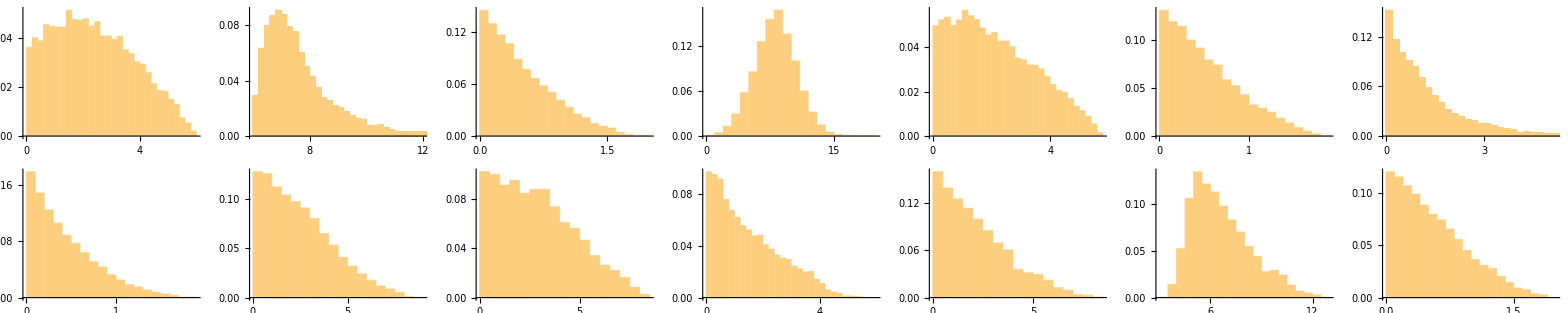

```mathematica
GraphicsGrid[ArrayReshape[Table[Histogram[QS1[[;;,i]],Automatic,"Probability"],{i,1,14}],{2,7}]]
```

```mathematica
GraphicsGrid[ArrayReshape[Table[ListPlot[QS1[[;;,i]],PlotStyle->Opacity[.1]],{i,1,14}],{2,7}]]
```

-Graphics-

```mathematica
us1=Map[(c.#)&,QS1];
```

```mathematica
StandardDeviation[us1]
```

96.516

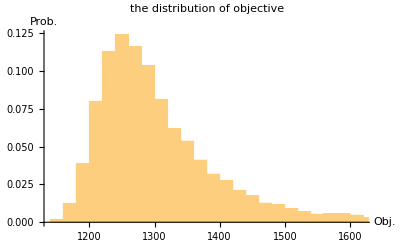

```mathematica
Histogram[us1,Automatic,"Probability",AxesLabel->{"Obj.","Prob."},PlotLabel->"the distribution of objective"]
```

```mathematica
Min[us1]
```

1142.93

```mathematica
ListPointPlot3D[QS1[[;;,1;;3]],AxesLabel->{"x_1","x_2","x_3"},PlotStyle->Opacity[.3],PlotLabel->"the scatter plot of the first three dimensions"]
```

-Graphics3D-

```mathematica
psrf[QS1]
```

{1.06656,1.05253,1.00405,1.04842,1.0843,1.00982,1.05834,1.00412,1.07403,1.15785,1.03356,1.10898,1.11605,1.01892}

```mathematica
psrf[QS]
```

{1.0843,1.00982,1.05834,1.00412,1.15785,1.03356,1.11605,1.01892}

```mathematica
QS//Dimensions
```

{100000,8}